```mathematica
(*The potential is V(x). Its support is [a,b]. We assume that m=hbar=1. c defines the interval for solving the Scoedinger equation*)
```

```mathematica
V[x_]:=1/Cosh[x]^2;
a=-10;
b=10;
c=4;
```

```mathematica
(*Here we solve the Schroedinger equation assuming that to the right of the potential (x>b) we have the outgoing wave of unit flux*)
```

```mathematica
SchrEq[k0_]:=Module[{k=k0},NDSolve[{-f''[x]/2+V[x]f[x]-k^2 f[x]==0,f[b]==Exp[I Sqrt[2]k b],f'[b]==I Sqrt[2] k Exp[I Sqrt[2] k b]},f,{x,a-c/k,b}]];
```

```mathematica
(*Here we find the wave function to the left of the potential (x<a). This is done by fitting the solution of the Schroedinger equation using the Exp[\pm ISqrt[2] k x] basis. step determines the number of points used for fitting. Note that we can find the wave function also by numerical differentiation.*)
```

```mathematica
step=1;
WaveFuncLeft[k0_]:=Module[{help=SchrEq[k0]},Fit[Table[Flatten[{x,f[x]/.help}],{x,a-c/k0,a,step/k0}],{Exp[I Sqrt[2]k0 x],Exp[-I Sqrt[2]k0 x]},x]];
```

```mathematica
(*Here we find the transmission coefficient -- it is determined by the coefficient in front of the incoming wave*)
```

```mathematica
T[k_]:=1/(WaveFuncLeft[k][[2]]/.x->0);
```

```mathematica
(*Now we check the solution using the exact result*)
```

```mathematica
t=Table[{k,Abs[T[k]]^2},{k,0.001,2,0.05}];
lp=ListPlot[t,PlotRange->All];
```

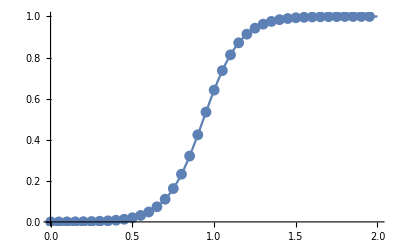

```mathematica
Show[Plot[Sinh[Pi Sqrt[2]x]^2/(Sinh[Pi Sqrt[2]x]^2+Cosh[Pi Sqrt[7]/2]^2),{x,0,2}],lp]
```